```mathematica
All Functions
```

```mathematica
frameExtract[videoFilename,skippedFrames,start,end,n];
chopper=Function[{image,gaussRout,gaussRin,gaussVert,binThres,sizeThres,horzExpand,vertExpand}];
cropper=Function[{image,chopped}];
imageToB64=Function[{picture}];
sendRequest=Function[{base64}];
combineLatex=Function[{outputFromAPI,croppedImageList}];
```

```mathematica
Live Demo
```

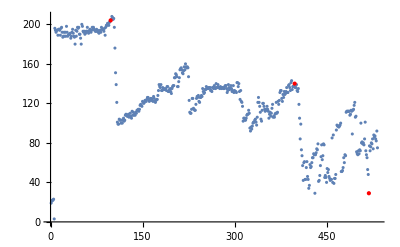

{-Graphics-,-Graphics-,-Graphics-}

```mathematica
boardImages=frameExtract["Lecture.mov",30,1,16000,3]
```

```mathematica
chopped=chopper[boardImages[[3]],40,30,9,0.035,800,10,10];
```

-Graphics-

-Graphics-

-Graphics-

-Graphics-

```mathematica
cropped=cropper[boardImages[[3]],chopped]
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
output=Table[sendRequest[imageToB64[cropped[[i]]]],{i,1,Length@cropped}]
```

{{,0,Sorry, we had trouble with that one. We work best with zoomed in, well cropped images of math.},{0,1,2,3,0.999872,},{x ( t ) = c _ { 1 } e ^ { - 4 t } + r _ { 2 } e ^ { - 3 t } + c _ { 3 } ^ { - 2 t },0.977703,},{x _ { 4 } \overline { e } ^ { - t } + c _ { 5 } + c _ { 6 } e ^ { t } + c _ { 7 } e ^ { 2 t },0.971103,},{+ c _ { 8 } e ^ { 3 t },0.959038,}}

```mathematica
combineLatex[output,cropped]
```

{$$0,1,2,3$$
$$x ( t ) = c _ { 1 } e ^ { - 4 t } + r _ { 2 } e ^ { - 3 t } + c _ { 3 } ^ { - 2 t }$$
$$x _ { 4 } \overline { e } ^ { - t } + c _ { 5 } + c _ { 6 } e ^ { t } + c _ { 7 } e ^ { 2 t }$$
$$+ c _ { 8 } e ^ { 3 t }$$,{-Graphics-}}